# Метод на най-малките квадрати (МНМК)

Задача: (a и b са съответно предпоследната и последната цифра от факултетния номер)
1. Да се състави таблицата (x_k, g(x_k)), където
x_k =  -b + k(0.1), k = OverBar[0,10],   g(x) = ⅇ^(((a+1)x)/10)
Търси се апроксимацията в точката s = -b + (0.17)a + 0.01. За тази цел:
2. Да се построи полином на ленейна регресия по получената таблица.
3. Да се построи полином на квадратична регресия по получената таблица.
4. Да се построи полином на кубична регресия по получената таблица.
5. Да се пресметне апроксимацията, използвайки всеки един от построените полиноми (общо 3).
6. Да се оцени грешката за всяка от получените апроксимации.
7. Да се направи сравнение между трите резултата.

## Генериране на данни

```mathematica
xt = Table[-7+k*0.1, {k, 0, 10}]
```

{-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.}

```mathematica
f[x_] := ⅇ^((7x)/10)
yt = f[xt]
```

{0.00744658,0.00798652,0.00856561,0.00918669,0.0098528,0.0105672,0.0113334,0.0121552,0.0130365,0.0139818,0.0149956}

```mathematica
P = Length[xt]
```

11

### Визуализация

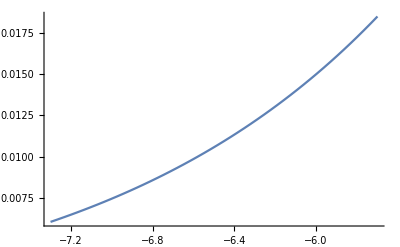

```mathematica
grf = Plot[f[x], {x, xt[[1]] - 0.3, xt[[P]] + 0.3}]
```

```mathematica
points = Table[{xt[[i]], yt[[i]]}, {i, 1, P}];
```

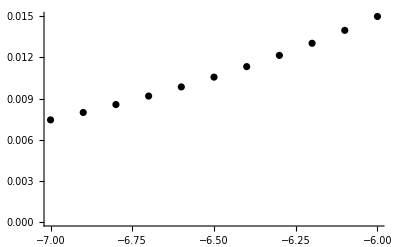

```mathematica
grp = ListPlot[points, PlotStyle->Black]
```

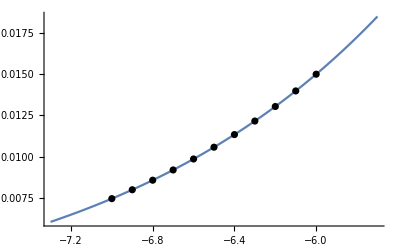

```mathematica
Show[grf, grp]
```

## Линейна регресия

### Попълваме таблицата

```mathematica
xt^2
```

{49.,47.61,46.24,44.89,43.56,42.25,40.96,39.69,38.44,37.21,36.}

```mathematica
yt*xt
```

{-0.0521261,-0.055107,-0.0582461,-0.0615508,-0.0650285,-0.0686868,-0.0725338,-0.0765776,-0.0808265,-0.0852889,-0.0899735}

### Намиране на сумите

```mathematica
∑_(i=1)^P xt[[i]]
```

-71.5

```mathematica
∑_(i=1)^P yt[[i]]
```

0.119108

```mathematica
∑_(i=1)^P xt[[i]]^2
```

465.85

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]
```

-0.765946

### Решаваме системата

```mathematica
A = ({{P, ∑_(i=1)^P xt[[i]]}, {∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2}}); b={∑_(i=1)^P yt[[i]], ∑_(i=1)^P yt[[i]]*xt[[i]]};
```

```mathematica
LinearSolve[A,b]
```

{0.0596113,0.00750512}

### Съставяме полинома

```mathematica
P1[x_] := 0.0596113 + 0.00750512x
```

Таен коз (възможност за самопроверка)

```mathematica
Fit[points, {1, x}, x]
```

0.0596113+0.00750512 x

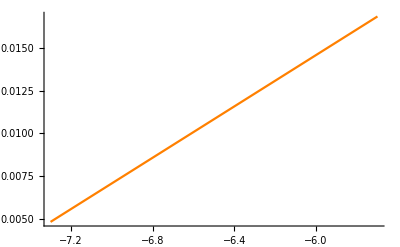

```mathematica
grfP1 = Plot[P1[x], {x, xt[[1]] - 0.3, xt[[P]] + 0.3}, PlotStyle->Orange]
```

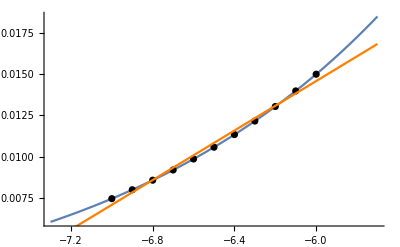

```mathematica
Show[grf, grp, grfP1]
```

```mathematica
P1[-5.97]
```

0.0148057

За сравнение истинската стойност

```mathematica
f[-5.97]
```

0.0153138

### Оценка на грешката

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^P (yt[[i]] - P1[xt[[i]]])^2)
```

0.000767618

#### Истинска грешка

```mathematica
Abs[f[-5.97] - P1[-5.97]]
```

0.00050808

## Квадратична регресия

### Попълваме таблицата

```mathematica
xt^2
```

{49.,47.61,46.24,44.89,43.56,42.25,40.96,39.69,38.44,37.21,36.}

```mathematica
yt*xt
```

{-0.0521261,-0.055107,-0.0582461,-0.0615508,-0.0650285,-0.0686868,-0.0725338,-0.0765776,-0.0808265,-0.0852889,-0.0899735}

```mathematica
xt^3
```

{-343.,-328.509,-314.432,-300.763,-287.496,-274.625,-262.144,-250.047,-238.328,-226.981,-216.}

```mathematica
xt^4
```

{2401.,2266.71,2138.14,2015.11,1897.47,1785.06,1677.72,1575.3,1477.63,1384.58,1296.}

```mathematica
yt*xt^2
```

{0.364883,0.380238,0.396074,0.41239,0.429188,0.446464,0.464217,0.482439,0.501124,0.520262,0.539841}

### Намиране на сумите

```mathematica
∑_(i=1)^P xt[[i]]
```

-71.5

```mathematica
∑_(i=1)^P yt[[i]]
```

0.119108

```mathematica
∑_(i=1)^P xt[[i]]^2
```

465.85

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]
```

-0.765946

```mathematica
∑_(i=1)^P xt[[i]]^3
```

-3042.33

```mathematica
∑_(i=1)^P xt[[i]]^4
```

19914.7

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]^2
```

4.93712

### Решаваме системата

```mathematica
A = ({{P, ∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2}, {∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3}, {∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4}}); b={∑_(i=1)^P yt[[i]], ∑_(i=1)^P yt[[i]]*xt[[i]],  ∑_(i=1)^P yt[[i]]*xt[[i]]^2};
```

```mathematica
LinearSolve[A,b]
```

{0.169855,0.0415066,0.0026155}

Таен коз (възможност за самопроверка)

```mathematica
Fit[points, {1, x, x^2}, x]
```

0.169855+0.0415066 x+0.0026155 x^2

### Съставяме полинома

```mathematica
P2[x_] := 0.169855 - 0.0415066x + 0.0026155 x^2
```

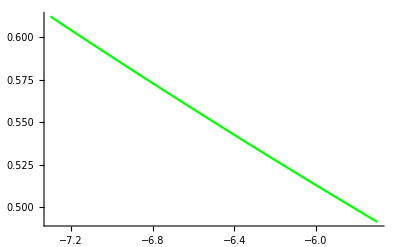

```mathematica
grfP2 = Plot[P2[x], {x, xt[[1]] - 0.3, xt[[P]] + 0.3}, PlotStyle->Green]
```

```mathematica
Show[grf,grp,grfP1, grfP2]
```

-Graphics-

```mathematica
P2[-5.97]
```

0.510868

За сравнение истинската стойност

```mathematica
f[-5.97]
```

0.0153138

### Оценка на грешката

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^P (yt[[i]] - P2[xt[[i]]])^2)
```

1.79172

#### Истинска грешка

```mathematica
Abs[f[-5.97] - P2[-5.97]]
```

0.495554

## Кубична регресия

### Попълваме таблицата

```mathematica
xt^2
```

{49.,47.61,46.24,44.89,43.56,42.25,40.96,39.69,38.44,37.21,36.}

```mathematica
yt*xt
```

{-0.0521261,-0.055107,-0.0582461,-0.0615508,-0.0650285,-0.0686868,-0.0725338,-0.0765776,-0.0808265,-0.0852889,-0.0899735}

```mathematica
xt^3
```

{-343.,-328.509,-314.432,-300.763,-287.496,-274.625,-262.144,-250.047,-238.328,-226.981,-216.}

```mathematica
xt^4
```

{2401.,2266.71,2138.14,2015.11,1897.47,1785.06,1677.72,1575.3,1477.63,1384.58,1296.}

```mathematica
yt*xt^2
```

{0.364883,0.380238,0.396074,0.41239,0.429188,0.446464,0.464217,0.482439,0.501124,0.520262,0.539841}

```mathematica
yt*xt^3
```

{-2.55418,-2.62364,-2.6933,-2.76302,-2.83264,-2.90202,-2.97099,-3.03937,-3.10697,-3.1736,-3.23904}

```mathematica
xt^5
```

{-16807.,-15640.3,-14539.3,-13501.3,-12523.3,-11602.9,-10737.4,-9924.37,-9161.33,-8445.96,-7776.}

```mathematica
xt^6
```

{117649.,107918.,98867.5,90458.4,82654.,75418.9,68719.5,62523.5,56800.2,51520.4,46656.}

### Намиране на сумите

```mathematica
∑_(i=1)^P xt[[i]]
```

-71.5

```mathematica
∑_(i=1)^P yt[[i]]
```

0.119108

```mathematica
∑_(i=1)^P xt[[i]]^2
```

465.85

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]
```

-0.765946

```mathematica
∑_(i=1)^P xt[[i]]^3
```

-3042.33

```mathematica
∑_(i=1)^P xt[[i]]^4
```

19914.7

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]^2
```

4.93712

```mathematica
∑_(i=1)^P xt[[i]]^5
```

-130659.

```mathematica
∑_(i=1)^P xt[[i]]^6
```

859185.

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]^3
```

-31.8988

### Решаваме системата

```mathematica
A= ({{P, ∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3}, {∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4}, {∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4, ∑_(i=1)^P xt[[i]]^5}, {∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4, ∑_(i=1)^P xt[[i]]^5, ∑_(i=1)^P xt[[i]]^6}}); b = {∑_(i=1)^P yt[[i]], ∑_(i=1)^P yt[[i]]*xt[[i]], ∑_(i=1)^P yt[[i]]*xt[[i]]^2, ∑_(i=1)^P yt[[i]]*xt[[i]]^3};
```

```mathematica
LinearSolve[A,b]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{11.,-71.5,465.85,-3042.33},{-71.5,465.85,-3042.33,19914.7},{465.85,-3042.33,19914.7,-130659.},{-3042.33,19914.7,-130659.,859185.}} may contain significant numerical errors.

{0.33634,0.118563,0.014487,0.000608794}

Таен коз (възможност за самопроверка)

```mathematica
Fit[points, {1, x, x^2,x^3}, x]
```

0.33634+0.118563 x+0.014487 x^2+0.000608793 x^3

### Съставяме полинома

```mathematica
P3[x_] :=0.33634 + 0.118563x + 0.014487 x^2 + 0.000608793 x^3
```

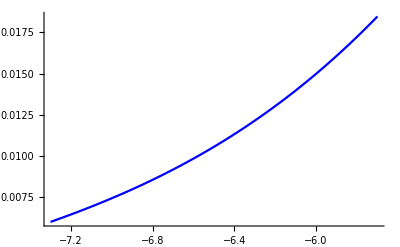

```mathematica
grfP3 = Plot[P3[x], {x, xt[[1]] - 0.3, xt[[P]] + 0.3}, PlotStyle-> Blue]
```

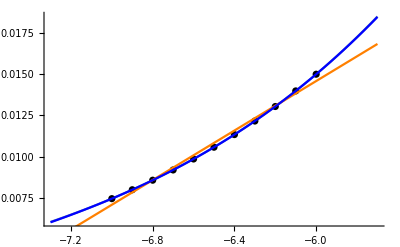

```mathematica
Show[grf, grp, grfP1,grfP2, grfP3]
```

### Намиране на приближена стойност (s = -b + (0.17)a + 0.01)

```mathematica
s = -7 + (0.17 * 6) + 0.01
```

-5.97

```mathematica
P3[-5.97]
```

0.015312

За сравнение истинската стойност

```mathematica
f[-5.97]
```

0.0153138

### Оценка на грешката

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^P (yt[[i]] - P3[xt[[i]]])^2)
```

2.17888×10^-6

#### Истинска грешка

```mathematica
Abs[f[-5.97] - P3[-5.97]]
```

1.85012×10^-6